```mathematica
RegionCentroid@CountryData["China",{"SchematicPolygon","Mercator"}]
```

{109.691,19.5945}

```mathematica
Function[{x,y},{(180Gudermannian[(π y)/180])/π,x}]@@{109.69105343569574,19.59452752503121}
```

{19.2234,109.691}

(0.434814 | 0.31267 | 0.163578 | 0.580002 | 0.806574 | 0.627132 | 0.816457 | 0.286038 | 0.426253 | 0.242922
0.396996 | 0.978686 | 0.695214 | 0.28142 | 0.29012 | 0.721054 | 0.0919018 | 0.706369 | 0.746327 | 0.161207
0.101851 | 0.213224 | 0.353565 | 0.421862 | 0.687099 | 0.547687 | 0.10484 | 0.653504 | 0.375526 | 0.987584
0.37656 | 0.701205 | 0.907154 | 0.625919 | 0.653084 | 0.95923 | 0.486595 | 0.25937 | 0.292945 | 0.699573)

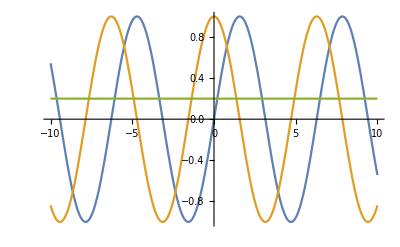

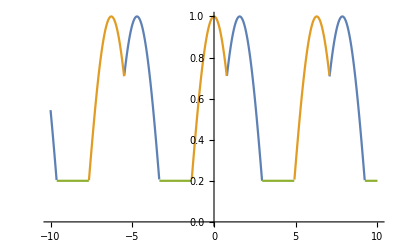

```mathematica
Plot[{Sin[x],Cos[x],0.2},{x,-10,10}]
M=Transpose@N@Table[{Sin[x],Cos[x],0.2},{x,-10,10,0.01}];
Pos[M_]:={#,First@SparseArray[UnitStep[M-#]]["AdjacencyLists"]}&@Max@M;
MaxData=Table[{i,#[[i,2]]}->#[[i,1]],{i,1,Length@#}]&@(Pos/@Transpose[M]);
ListData=SparseArray@Join[MaxData,{{_,_}->Null}];
ListLinePlot[Transpose@ListData,DataRange->{-10,10}]
```

{6.42469/(1+(-4.18422+x)^2)+4.43908/(1+(-1.98272+x)^2)+2.96052/(1+(2.16541+x)^2),4.59795/(1+(-2.00827+x)^2)+9.49542/(1+(0.3939+x)^2)+8.92336/(1+(1.28282+x)^2),6.06138/(1+(-1.78969+x)^2)+1.91536/(1+(-1.45377+x)^2)+8.08015/(1+(4.15838+x)^2)}

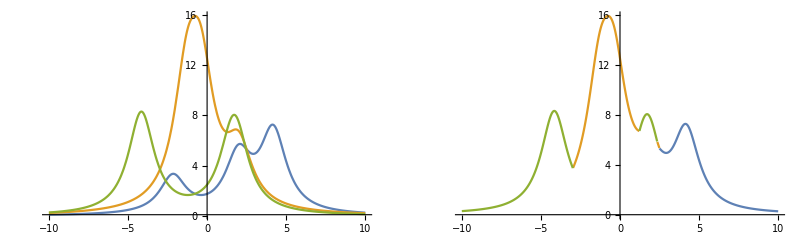

```mathematica
Fun=Table[Inner[Function[{a,b},a/(1+(x-b)^2)],RandomReal[10,3],RandomReal[{-5,5},3],Plus],{i,1,3}]
M=Transpose@N@Table[Fun,{x,-10,10,0.01}];
Pos[M_]:={#,First@SparseArray[UnitStep[M-#]]["AdjacencyLists"]}&@Max@M;
MaxData=Table[{i,#[[i,2]]}->#[[i,1]],{i,1,Length@#}]&@(Pos/@Transpose[M]);
ListData=SparseArray@Join[MaxData,{{_,_}->Null}];
GraphicsRow[{Plot[Fun,{x,-10,10},PlotRange->All],ListLinePlot[Transpose@ListData,DataRange->{-10,10},PlotRange->All]},ImageSize->Full]
```

```mathematica
MaxData
```

{{1,2}→0.24262,{2,2}→0.243229,{3,2}→0.243841,{4,2}→0.244456,{5,2}→0.245072,{6,2}→0.245692,{7,2}→0.246313,{8,2}→0.246938,{9,2}→0.247564,{10,2}→0.248193,{11,2}→0.248825,{12,2}→0.249459,{13,2}→0.250096,{14,2}→0.250735,{15,2}→0.251377,{16,2}→0.252022,{17,2}→0.252669,1968,{1986,2}→0.270801,{1987,2}→0.270098,{1988,2}→0.269398,{1989,2}→0.268701,{1990,2}→0.268007,{1991,2}→0.267315,{1992,2}→0.266626,{1993,2}→0.26594,{1994,2}→0.265257,{1995,2}→0.264576,{1996,2}→0.263899,{1997,2}→0.263223,{1998,2}→0.262551,{1999,2}→0.261881,{2000,2}→0.261214,{2001,2}→0.260549}
 |  |  |  |